```mathematica
css zebrafinch model;
ns is number of stressed juveniles;
nh is number of health juveniles;
NNA is number of adapted adults;
NNn is number of nonadapted adults;

ba: benefit of adaptive behavior on fecundity;
bn: benefit of non-adaptive behavior on fecundity;
pa: probability an adapted adult produces stressed offspring;
pn: probability a nonadapted adult produces stressed offspring;
vs: vitality (opposite of mortality rate) of a stresed juvenille;
vh: vitality (opposite of mortality rate) of a healthy juvenille;
vI: mortality cost of ndividual learning;
lsO : frequency of oblique learners who were stressed juveniles;
lhO : frequency of oblique learners who were healthy juveniles;


Recursions;
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs((1-lsO) vI z +lsO qO ) + nh vh((1-lhO) vI z +lhO qO );
NNn :=ns vs((1-lsO) vI (1-z)+lsO(1- qO) ) + nh vh((1-lhO) vI (1-z)+lhO(1- qO) );
qO := (1-u)(Na/(Na +Nn));
```

```mathematica
Transition Matrix;
(*leave Q in matrix below different than one up above recursions*)
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs((1-lsO) vI z +lsO Qh), vh((1-lhO) vI z +lhO Qh ), 0, 0}, {vs((1-lsO) vI (1-z)+lsO(1- Qh) ), vh((1-lhO) vI (1-z)+lhO(1- Qh) ), 0, 0}})
```

```mathematica
convert to frequencies and make sure they sum to one;
```

```mathematica
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
solve Q-hat for common strategy;
Fasols=Solve[FFa==Fa,Fa];
```

```mathematica
Graphing for non-Softmax Version;
(* begin looping here, try matrices*)
PSTYLE={Directive[RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862]],Directive[RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961]],Directive[RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]],Directive[RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961]],Directive[RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253]],Directive[RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],Dashed],Directive[RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],Dashed],Directive[RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],Dashed],Directive[RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],Dashed],Directive[RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],Dashed]};
ulist={0.01,0.05,0.15, 0.25 , 0.5};
blist={1.5,2,3,5};
lsOstart=0.5;
lhOstart=0.01;
imax=4000;
lhOtab=lsOtab=Table[0,{i,imax-1}];
delta=0.08;
lsOtab[[1]]=lsOstart;
lhOtab[[1]]=lhOstart;
```

```mathematica
For[j=1,j≤Length[blist],j++,{
For[h=1,h≤Length[ulist],h++,{
subs = {ba->blist[[j]],bn->1,z->0.8,vs->.8,vh->1,vI->0.8 ,u->ulist[[h]] , pa -> 0, pn-> 1};
(*solve for qhat*)
QHAT[LHO_,LSO_] :=Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI} /.subs];
AA2=AA/.subs;
LL=Eigenvalues[AA2];
(*isolate Dominant eigenvalue, substitute in q-hat *)
Lambda1[ lsO_, lhO_,LHO_,LSO_]:= Simplify[LL[[2]]/.Qh->  QHAT[LHO,LSO]];
(*take partial derivatives to calculate gradient, substitute mutant for common type*)
DlsO=D[Lambda1[lsO, lhO,LHO,LSO],lsO]/. {LHO -> lhO,LSO-> lsO};
DlhO=D[Lambda1[lsO, lhO,LHO,LSO],lhO]/. {LHO -> lhO,LSO-> lsO};
(*graph*)

For[i=2,i<imax,i++,{
lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];
}];
lsOtab1=If[h==1,lsOtab,lsOtab1];
lsOtab2=If[h==2,lsOtab,lsOtab2];
lsOtab3=If[h==3,lsOtab,lsOtab3];
lsOtab4=If[h==4,lsOtab,lsOtab4];
lsOtab5=If[h==5,lsOtab,lsOtab5];
lhOtab1=If[h==1,lhOtab,lhOtab1];
lhOtab2=If[h==2,lhOtab,lhOtab2];
lhOtab3=If[h==3,lhOtab,lhOtab3];
lhOtab4=If[h==4,lhOtab,lhOtab4];
lhOtab5=If[h==5,lhOtab,lhOtab5];
}];


plotcode=ListLinePlot[{lhOtab1,lhOtab2,lhOtab3,lhOtab4,lhOtab5, lsOtab1,lsOtab2,lsOtab3,lsOtab4,lsOtab5},PlotLabels->ulist,PlotRange->{All,{0,1}},PlotStyle->PSTYLE,AxesLabel->{time, freq oblique},PlotLegends->{Placed[PointLegend[ulist],Bottom],Placed[LineLegend[{Normal,Dashed},{"healthy juv","stressed juv"}],Top]},PlotLabel->subs, ImageSize->440];

p1 = If[j≠1,p1,plotcode];
       p2 = If[j≠2,p2,plotcode];
       p3 = If[j≠3,p3,plotcode];
       p4 = If[j≠4,p4,plotcode];
}];
```

SetDelayed::write: Tag Root in Root[-0.2 lhO+0.2 lsO+«12»+(-0.44+0.4 lhO-0.06 lsO-(0.233333 lhO)/Plus[«3»]+(0.333333 lhO LHO)/Plus[«3»]+(0.0233333 lsO)/Plus[«3»]-(0.0333333 LHO lsO)/Plus[«3»]-(0.0833333 lhO LSO)/Plus[«3»]+(0.00833333 lsO LSO)/Plus[«3»]-(0.166667 lhO √Plus[«6»])/Plus[«3»]+(0.0166667 lsO √Plus[«6»])/Plus[«3»]) #1^2+0.2 #1^4&,2][lsO_,lhO_,LHO_,LSO_] is Protected.

$Aborted

```mathematica
Grid[{{p1,p2,p3,p4}} ]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[ "lhIinvade.pdf",Grid[{{p1,p2,p3,p4}} ]]
```

lhIinvade.pdf

```mathematica
Plots for individual graphs, non-softmax;
```

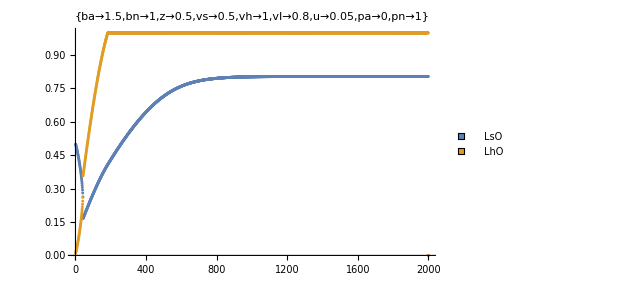

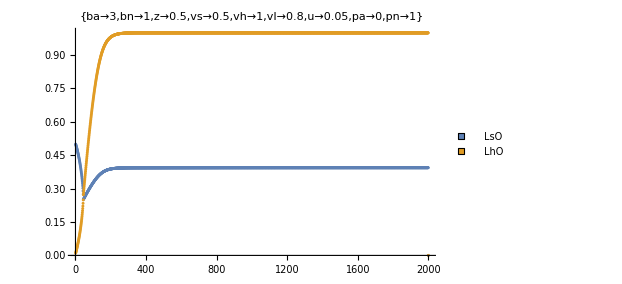

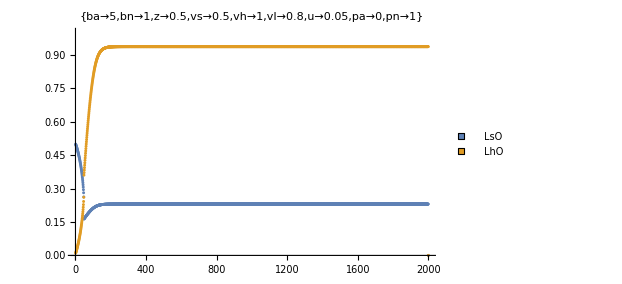

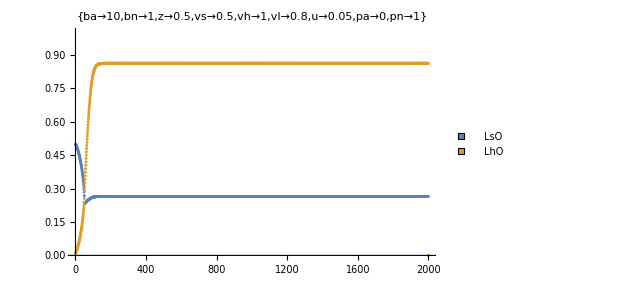

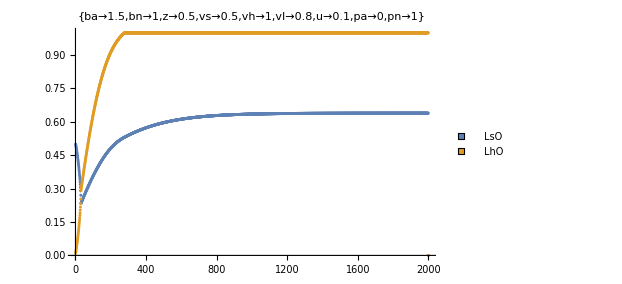

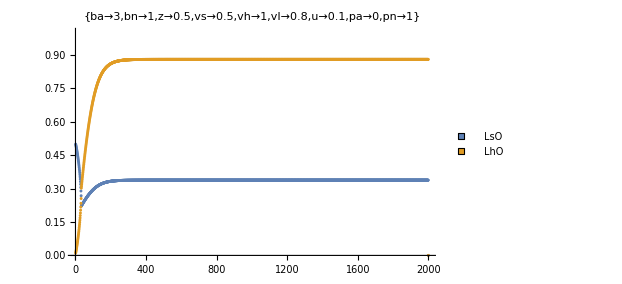

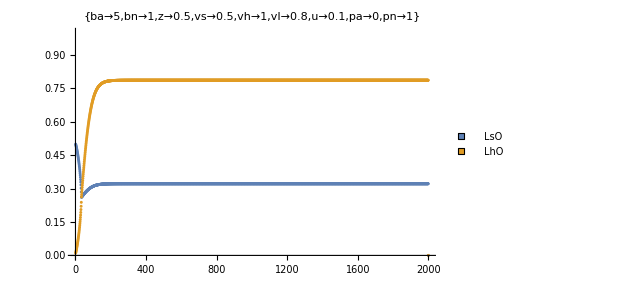

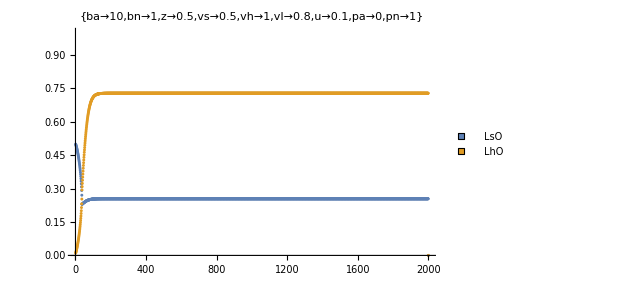

```mathematica
(*individual plots not in a grid*)
(* begin looping here*)
ulist={0.05,0.1, 0.2 };
blist={1.5,3,5,10};
lsOstart=0.5;
lhOstart=0.01;
imax=2000;
For[h=1,h≤Length[ulist],h++,{
For[j=1,j≤Length[blist],j++,{
subs = {ba->blist[[j]],bn->1,z->.5,vs->.5,vh->1,vI->.8  ,u->ulist[[h]] , pa -> 0, pn-> 1};
test = {lsO->0 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2};
(*solve QHAT for home condition, with frequecies as parameters*)
QHAT[LHO_,LSO_] :=Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI} /.subs];
(*isolate dominant eigenvalue*)
AA2=AA/.subs;
LL=Eigenvalues[AA2];
(*isolate Dominant eigenvalue, substitute in q-hat *)
Lambda1[ lsO_, lhO_,LHO_,LSO_]:= Simplify[LL[[2]]/.Qh->  QHAT[LHO,LSO]];
(*take partial derivatives to calculate gradient, substitute mutant for common type*)
DlsO=D[Lambda1[lsO, lhO,LHO,LSO],lsO]/. {LHO -> lhO,LSO-> lsO};
DlhO=D[Lambda1[lsO, lhO,LHO,LSO],lhO]/. {LHO -> lhO,LSO-> lsO};
(*graph*)
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
delta=0.08;
lsOtab[[1]]=lsOstart;
lhOtab[[1]]=lhOstart;
DlsOtab[[1]]=DlsO/.subs/.{lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.subs/.{lsO->lsOstart,lhO->lhOstart};
For[i=2,i<imax,i++,{

lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

DlsOtab[[i]]=DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
}];

Print[ListPlot[{lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLegends->PointLegend[{LsO,LhO},LegendMarkers->Graphics[Rectangle[]]],PlotLabel->subs, ImageSize->460]];
}]
}];
```